```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Needs["ErrorBarPlots`"]
```

DropInList lässt das von einer Liste list mit inneren Listen jedes Element von from bis to fallen (jeweils inklusive)

```mathematica
DropInList[list_,from_,to_]:=Module[{buffer=list}, For[i=0,i<Length[buffer],i++;buffer[[i]]=Drop[buffer[[i]],{from,to}]];If[from⩽to,
Return[buffer],Return["It has to be from =< to"]]]
```

ErrorBarXY erzeugt eine Liste mit ErrorBar[x[[i]],y[[i]]]
Alternativ: ErrorBarXY[listXerr_,listYerr_]=ErrorBar@@@(Partition[Flatten[Riffle[listXerr,listYerr]],2])

```mathematica
ErrorBarXY[listXerr_,listYerr_]:=Module[{buffer=listXerr}, For[i=0,i<Length[buffer],i++;buffer[[i]]=ErrorBar[listXerr[[i]],listYerr[[i]]]]; If[Length[listXerr]==Length[listYerr],
Return[buffer],Return["Length of lists not equal"]]]
```

errorPlotValue erzeugt die Punkte aus listX und listY und hängt jedem Punkt die entsprechende Errorbar[listXerr,listYerr] an

```mathematica
errorPlotValue[listX_,listY_,listXerr_,listYerr_]:=Module[{buffer=listXerr,errors,points,plotValues}, errors=ErrorBarXY[listXerr,listYerr];
points=Partition[Flatten[Riffle[listX,listY]],2];
plotValues=Partition[Riffle[points,errors],2]; If[Length[listXerr]==Length[listYerr]==Length[listX]==Length[listY],
Return[plotValues],Return["Length of lists not equal"]]]
```

errorPropNew ist für die Fehlerfortpflanzung ganzer Listen geeignet. vars={{x,dx},{y,dy}...} und func eine Funktion die von x,y... abhängt. Es wird die zugehörige Fehlerfunktion zurückgegeben. Speicher diese unter einem Namen ab zB errFkt.
Nutze errFkt[f, list_x,list_dx,list_y,list_dy,...]

```mathematica
errorPropNew[func_,vars_]:=Module[{derivs=Table[0,{Length[vars]}],funcErrorForm,parameter,errFunction},

For[ii=1,ii≤Length[vars],ii++,derivs[[ii]]=D[func,vars[[ii,1]]];];
parameter=Flatten[vars];
funcErrorForm=Sqrt[Sum[(derivs[[ii]]*vars[[ii,2]])^2,{ii,Length[vars]}]];
errFunction=Function@@{parameter,funcErrorForm};
Return[errFunction];];
```

Wendet f auf die n-te Komponenten jedes Punktes in g an. Alternativ {f@First[#], Last[#]} &/@ g;

```mathematica
(*  MapAt[(f[#])&,#,n]&/@g   *)
```

## Beispiel: C16

## M1

### Messwerte

```mathematica
messwerte1=({{24.6, 30.3, 35.5, 40.0, 45.0, 50.0, 55.0, 60.0, 65.0, 70.0, 75.0, 80.0, 85.0, 90.0, 95.0, 100.0, 105.0, 110.0, 115.0, 120.0, 125.0, 130.0, 135.4, 140.0, 145.0, 150.0, 155.0, 160.0, 165.0, 170.0}, {1.693, 1.344, 1.090, 0.902, .745, .606, .503, .416, .347, .289, .241, .203, .171, .143, .121, .104, .086, .076, .065, .057, .049, .042, .036, .032, .029, .025, .022, .019, .017, .015}});
```

```mathematica
c=20 *10^-3;
b=10*10^-3;
d=1*10^-3;
```

```mathematica
i1=2.0*10^-3;
```

```mathematica
di1=1.0*10^-3;
```

```mathematica
kB=1.3806504*^-23 ;
```

```mathematica
f[x_]:=x+273.15;
```

```mathematica
messwerte1t=Transpose[messwerte1] ;
```

```mathematica
messwerte1si=MapAt[(f[#])&,#,1]&/@messwerte1t;
```

```mathematica
messwerte1si //MatrixForm ;
```

```mathematica
u1=Transpose[messwerte1si][[2]];
```

```mathematica
leitf[U_]:=i1/U*c/(b *d);
```

```mathematica
leitf1=leitf[#]&/@Transpose[messwerte1si][[2]];
```

```mathematica
g[x_]:=Log[x];
```

```mathematica
leitf1ln=g[#]&/@leitf1;
```

```mathematica
g1[x_]:=1/(2 kB x);
```

```mathematica
messwerte1xaxis=g1[#]&/@Transpose[messwerte1si][[1]];
```

### Fehler

4 stellig U bis 9.999V Auflösung 0.001V Fehler (.5% + 3dgts)

```mathematica
messfehler1u[x_]:=0.001*3+x*0.005;
```

```mathematica
fehler1u=messfehler1u[#] & /@ u1;
```

```mathematica
errorPropNew[Log[I1/U*c/(b *d)],{{U,dU},{I1,dI1}}]
```

Function[{U,dU,I1,dI1},√(dI1^2/I1^2+dU^2/U^2)]

```mathematica
leitf1Err=errorPropNew[I1/U*c/(b *d),{{U,dU},{I1,dI1}}]@@{u1,fehler1u,i1,di1};
```

```mathematica
leitf1lnErr=errorPropNew[Log[I1/U*c/(b *d)],{{U,dU},{I1,dI1}}]@@{u1,fehler1u,i1,di1};
```

```mathematica
messfehler1T[x_]:=3+x*0.02;
```

```mathematica
T1GradErr=messfehler1T[#] & /@messwerte1[[1]];
```

```mathematica
errorPropNew[1/(2 kB t),{{t,dt}}];
```

```mathematica
T1K=Transpose[messwerte1si][[1]];
```

```mathematica
messwerte1xaxisErr=errorPropNew[1/(2 kB t),{{t,dt}}]@@{T1K,T1GradErr};
```

### Plotten (Vorbereitung)

```mathematica
points1=Partition[Flatten[Riffle[messwerte1xaxis,leitf1ln]],2];
```

```mathematica
Length[messwerte1xaxis];
```

```mathematica
errors1=Table[ErrorBar[messwerte1xaxisErr[[i ]],leitf1lnErr[[i]]],{i,1,30}];
```

```mathematica
plotValues1=Partition[Riffle[points1,errors1],2];
```

```mathematica
errPlot1=ErrorListPlot[plotValues1,AxesLabel->{"1/(2 SubscriptBox[k, B] T) in 1/J","ln(σ) inA/(V m)"},PlotRange->Full]
```

-Graphics-

```mathematica
messwerte1xaxisErr/messwerte1xaxis;
```

```mathematica
leitf1lnErr/leitf1ln;
```

### Fit (Berechnung)

```mathematica
lmXYErr=LinearModelFit[points1,x,x,Weights->1/(leitf1lnErr^2+(1.1944109069154434*^-19)^2*messwerte1xaxisErr^2),IncludeConstantBasis->True];
```

```mathematica
lmYErr=LinearModelFit[points1,x,x,Weights->1/leitf1lnErr^2,IncludeConstantBasis->True];
```

```mathematica
Show[errPlot1, Plot[{Normal[lmYErr]},{x,0,10^21}, PlotLegends->{"Y Error: " <> ToString[lmYErr["BestFit"]]},PlotStyle->{Black}]]
```

-Graphics-

```mathematica
lmYErr[{"BestFit","ParameterTable","ANOVATable","RSquared","AdjustedRSquared"}]
```

{15.2786-1.19441×10^-19 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | 15.2786 | 0.0648676 | 235.534 | 1.03327×10^-47
x | -1.19441×10^-19 | 6.48191×10^-22 | -184.268 | 9.93657×10^-45, | DF | SS | MS | F-Statistic | P-Value
x | 1 | 228.278 | 228.278 | 33954.8 | 9.93657×10^-45
Error | 28 | 0.188244 | 0.00672299 |  | 
Total | 29 | 228.466 |  |  | ,0.999176,0.999147}

```mathematica
Show[errPlot1, Plot[{Normal[lmXYErr]},{x,0,10^21}, PlotLegends->{"XY Error: " <> ToString[lmNew["BestFit"]]},PlotStyle->{Black}]]
```

-Graphics-

```mathematica
lmXYErr[{"BestFit","ParameterTable","ANOVATable","RSquared","AdjustedRSquared"}]
```

{15.2822-1.19476×10^-19 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | 15.2822 | 0.064698 | 236.208 | 9.53933×10^-48
x | -1.19476×10^-19 | 6.47398×10^-22 | -184.549 | 9.52249×10^-45, | DF | SS | MS | F-Statistic | P-Value
x | 1 | 208.261 | 208.261 | 34058.3 | 9.52249×10^-45
Error | 28 | 0.171215 | 0.00611484 |  | 
Total | 29 | 208.432 |  |  | ,0.999179,0.999149}

```mathematica
Exp[15.282159935452153]
```

4.33469×10^6

```mathematica
errorPropNew[Exp[x],{{x,dx}}]@@{15.282159935452153,0.06469799300769175}
```

280446.

```mathematica
%/10^6
```

0.280446

E_G= (1.19441+-0.006481)*10^-19 nur X Gewicht

E_G= (1.1948+-0.0065)*10^-19 X und Y Gewicht und σ_0= (4.33 +- 0.28 )×10^6

```mathematica
0.0065/1.1948
```

0.00544024

```mathematica
(.28)/4.33
```

0.0646651

## SLOT Versuch 2

### Messwerte

```mathematica
kontrast[iMax_,iMin_]:= (iMax - iMin)/(iMax + iMin)
```

```mathematica
resolutionUSAF[gruppe_,element_]:=2^(gruppe+(element -1)/6)
```

```mathematica
l=Table[i,{i,1,6}];
```

```mathematica
jn24502jnMinusdIIIgruppe2=({{556, 69}, {401, 50}, {433, 56}, {459, 59}, {469, 65}, {474, 78}});
```

```mathematica
jn24502jnMinusdIIIgruppe3=({{405, 74}, {418, 80}});
```

```mathematica
jn24502jnMinusdgruppe2=({{563, 68}, {421, 56}, {459, 57}, {491, 57}, {508, 58}, {500, 72}});
```

```mathematica
jn24502jnMinusdgruppe3=({{310, 81}, {372, 130}});
```

```mathematica
jn24502nnMinusdIIIgruppe2=({{449, 178}, {329, 166}, {339, 185}, {338, 219}, {330, 237}, {325, 260}});
```

```mathematica
jn24502nnMinusdIIIgruppe3=({{317, 250}, {334, 276}});
```

```mathematica
jn24502nnMinusdgruppe2=({{395, 227}, {302, 209}, {306, 241}, {326, 260}, {313, 274}, {307, 293}});
```

```mathematica
jn24502nnMinusdgruppe3=({{305, 265}, {311, 300}});
```

```mathematica
linien2={jn24502jnMinusdIIIgruppe2,jn24502jnMinusdgruppe2,jn24502nnMinusdIIIgruppe2,jn24502nnMinusdgruppe2};
```

```mathematica
linien3={jn24502jnMinusdIIIgruppe3,jn24502jnMinusdgruppe3,jn24502nnMinusdIIIgruppe3,jn24502nnMinusdgruppe3};
```

```mathematica
yAllgemein=Table[Join[kontrast@@@linien2[[n]],kontrast@@@linien3[[n]]],{n,1,Length[linien2]}];//N
```

```mathematica
xAllgemein=Table[Join[resolutionUSAF[2,#]&/@Table[i,{i,1,Length[jn24502jnMinusdIIIgruppe2]}],resolutionUSAF[3,#]&/@Table[i,{i,1,Length[jn24502jnMinusdIIIgruppe3]}]],{n,1,Length[linien2]}];//N
```

### Plotten Allgemein

```mathematica
SLOTpointsAllgemein=Table[Partition[Flatten[Riffle[xAllgemein[[i]],yAllgemein[[i]]]],2],{i,1,4}];
```

```mathematica
SLOTxErr=Table[0,{i,1,8}];
```

```mathematica
SLOTyErr=Table[0,{i,1,8}];
```

```mathematica
SLOTerr=Table[ErrorBar[SLOTxErr[[i ]],SLOTyErr[[i]]],{i,1,8}];
```

```mathematica
plotSLOTAllgemein=Table[Partition[Riffle[SLOTpointsAllgemein[[i]],SLOTerr],2],{i,1,4}];
```

```mathematica
legendeAllgemein={"jn24502jnMinusdIIIgruppe2","jn24502jnMinusdgruppe2","jn24502nnMinusdIIIgruppe2","jn24502nnMinusdgruppe2"}
```

{jn24502jnMinusdIIIgruppe2,jn24502jnMinusdgruppe2,jn24502nnMinusdIIIgruppe2,jn24502nnMinusdgruppe2}

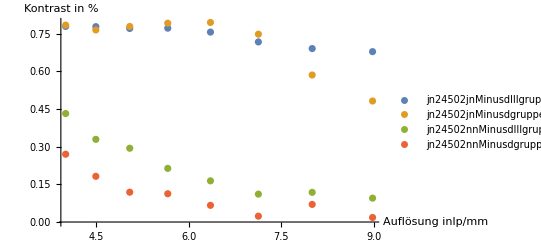

```mathematica
errPlotAllgemein=ErrorListPlot[plotSLOTAllgemein,AxesLabel->{"Auflösung inlp/mm","Kontrast in %"},PlotRange->Full,PlotLegends-> legendeAllgemein]
```

## Ausprobieren

### Listen für jn und nn

```mathematica
y2=kontrast@@@jn24502jnMinusdIIIgruppe2//N
```

{0.7792,0.778271,0.770961,0.772201,0.756554,0.717391}

```mathematica
x2=resolutionUSAF[2,#]&/@l //N
```

{4.,4.48985,5.03968,5.65685,6.3496,7.12719}

```mathematica
y3=kontrast@@@jn24502jnMinusdIIIgruppe3//N
```

{0.691023,0.678715}

```mathematica
x3=resolutionUSAF[3,#]&/@Table[i,{i,1,2}] //N
```

{8.,8.9797}

```mathematica
x=Join[x2,x3]
```

{4.,4.48985,5.03968,5.65685,6.3496,7.12719,8.,8.9797}

```mathematica
y=Join[y2,y3]
```

{0.7792,0.778271,0.770961,0.772201,0.756554,0.717391,0.691023,0.678715}

### Plot jn

```mathematica
SLOTpoints=Partition[Flatten[Riffle[x,y]],2];
```

```mathematica
Length[x]
```

8

```mathematica
SLOTxErr=Table[0,{i,1,8}];
```

```mathematica
SLOTyErr=Table[0,{i,1,8}];
```

```mathematica
SLOTerr=Table[ErrorBar[SLOTxErr[[i ]],SLOTyErr[[i]]],{i,1,8}];
```

```mathematica
plotSLOT=Partition[Riffle[SLOTpoints,SLOTerr],2];
```

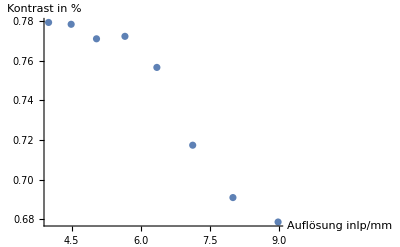

```mathematica
errPlot1=ErrorListPlot[plotSLOT,AxesLabel->{"Auflösung inlp/mm","Kontrast in %"},PlotRange->Full]
```

### Plot nn

```mathematica
Ny2=kontrast@@@jn24502nnMinusdIIIgruppe2//N
```

{0.432217,0.329293,0.293893,0.213645,0.164021,0.111111}

```mathematica
Nx2=resolutionUSAF[2,#]&/@l //N
```

{4.,4.48985,5.03968,5.65685,6.3496,7.12719}

```mathematica
Ny3=kontrast@@@jn24502nnMinusdIIIgruppe3//N
```

{0.118166,0.095082}

```mathematica
Nx3=resolutionUSAF[3,#]&/@Table[i,{i,1,2}] //N
```

{8.,8.9797}

```mathematica
Nx=Join[Nx2,Nx3]
```

{4.,4.48985,5.03968,5.65685,6.3496,7.12719,8.,8.9797}

```mathematica
Ny=Join[Ny2,Ny3]
```

{0.432217,0.329293,0.293893,0.213645,0.164021,0.111111,0.118166,0.095082}

```mathematica
NSLOTpoints=Partition[Flatten[Riffle[Nx,Ny]],2];
```

```mathematica
SLOTxErr=Table[0,{i,1,8}];
```

```mathematica
SLOTyErr=Table[0,{i,1,8}];
```

```mathematica
NSLOTerr=Table[ErrorBar[SLOTxErr[[i ]],SLOTyErr[[i]]],{i,1,8}];
```

```mathematica
NplotSLOT=Partition[Riffle[NSLOTpoints,NSLOTerr],2];
```

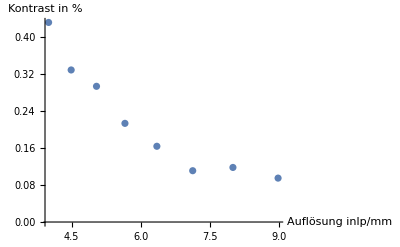

```mathematica
NerrPlot1=ErrorListPlot[NplotSLOT,AxesLabel->{"Auflösung inlp/mm","Kontrast in %"},PlotRange->Full]
```